```mathematica
Needs["ExperimentEvaluation`"]
SetDirectory["~"];
problemRewrite={"gp.demo.SymbolicRegression"->"1D","gp.demo.SymbolicRegression2D"->"2D","gp.demo.SymbolicRegression3D"->"3D","gp.demo.SymbolicRegression4D"->"4D","gp.demo.Maze"->"M1","gp.demo.MazeRangeFinders"->"M2"};
solverLabelRewrite={"SOLVER",{"GPAT"->"AT","GP"->"G","NEAT"->"N"}};
functionImplRewrite={"gpat.ATFunctions$"->"N","gpat.ATFunctionsNoConsts$"->"NC","gpat.ATFunctionsLikeGP$"->"GP","gpat.ATFunctionsLocks$"->"L","gpat.ATFunctionsComplexifyOnly$"->"CO","gpat.ATFunctionsAllConsts$"->"AC"};
functionImplLabelRewrite={"GPAT.FUNCTION_IMPL",functionImplRewrite};
distanceLabelRewrite={"GPAT.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};
distanceGeneralKLabelRewrite={"GP.DISTANCE_GENERAL_K",{}};
distanceGeneralAlphaLabelRewrite={"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"true"->"1","false"->"0"}};
distanceGeneralBetaLabelRewrite={"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"true"->"1","false"->"0"}};
distanceGeneralC1LabelRewrite={"GPAT.DISTANCE_C1",{}};
distanceGeneralC2LabelRewrite={"GPAT.DISTANCE_C2",{}};
distanceGeneralCACTLabelRewrite={"GPAT.DISTANCE_CACT",{}};
plotRange={All,{0,100}};
listOfDirectProblems=Grid[{{#[[1]]},{Style[TraditionalForm[#[[2]]],FontSize->12]}}]&/@{{"1D-F",1.5 Subscript[x, 1]^3+2.3 Subscript[x, 1]^2-1.1 Subscript[x, 1]+3.7},{"1D-H",0.1 Subscript[x, 1]^2+0.2Sin[Subscript[x, 1]]},{"2D-I",1.5 Subscript[x, 1] Subscript[x, 2]^2+2.3 Subscript[x, 1] Subscript[x, 2]-1.1 Subscript[x, 2]^2},{"2D-K",Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1] Subscript[x, 2]-Subscript[x, 2]^2},{"3D-E",1.5 Subscript[x, 1] Subscript[x, 2]+2.3 Subscript[x, 1]+Subscript[x, 2] Subscript[x, 3]-1.1 Subscript[x, 3]},{"3D-H",1.5 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]+2.3 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]-1.1 Subscript[x, 2]+5.3},{"3D-K",Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 2]+Subscript[x, 2] Subscript[x, 3]},{"4D-C",1.5 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3] Subscript[x, 4]},{"4D-F",1.5 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]+2.3 Subscript[x, 1]-1.1 Subscript[x, 2]-1.1 Subscript[x, 4]},{"4D-G",1.5 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3] Subscript[x, 4]+2.3 Subscript[x, 1]-1.1 Subscript[x, 2]},{"4D-V",Exp[-1.36709 Subscript[x, 2]^2] Subscript[x, 1](2.43454 Exp[-Subscript[x, 3]^2] -0.393788 Sin[1-Subscript[x, 1]])},{"MAZE-1",""},{"MAZE-2",""}};
listOfDirectProblems={"1D-F","1D-H","2D-I","2D-K","3D-E","3D-H","3D-K","4D-C","4D-F","4D-G","4D-V","MAZE-1","MAZE-2"};
listOfIndirectProblems={"Bit Reverse","Bit Shift","Bit Rotate","Parity","Visual Discrimination","Mobile Robot Navigation"};
```

```mathematica
a=8.1;
b=5.6;
all=600;
testFisherExact[{{0.01a all,all-0.01a all},{0.01b all,all-0.01b all}}]
```

0.109128

## Experiments GPAT Direct Innovation Numbers

```mathematica
names={"T/AT_B_OR","T/AT_B_NC","T/AT_B_GP","T/AT_B_AC","T/AT_B_CO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE_C2","GPAT.DISTANCE_C1","GPAT.DISTANCE_CACT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite,
distanceGeneralC1LabelRewrite,
distanceGeneralC2LabelRewrite,
distanceGeneralCACTLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","RECO.GENERATOR","PROBLEM","GPAT.DISTANCE_CACT","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
printAsTable[sortedData,changingParameters[data]];
```

{GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
parts = 81;
cellAll={};
colNumber=3;
(*parts = 27;
cellAll={};
colNumber=1;*)

selectedData=selectData[sortedData,{"PROBLEM"->{"1D"},"SYMBOLIC_REGRESSION.F"->{"F"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["1DF",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"1D"},"SYMBOLIC_REGRESSION.F"->{"H"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["1DH",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"2D"},"SYMBOLIC_REGRESSION.F"->{"I"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["2DI",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"2D"},"SYMBOLIC_REGRESSION.F"->{"K"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["2DK",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"E"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DE",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"H"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DH",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"K"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DK",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"C"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DC",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"F"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DF",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"G"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DG",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"V"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DV",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"M1"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["M1",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"M2"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["M2",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["AT_B_DIRECT.pdf",Grid[cellAll,Frame->All]];*)
Export["AT_B_DIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"",Style["GPAT Innovation Numbers: Success, Constants, Nodes, Depth",FontSize->25]},#},Frame->All]]&/@cellAll
```

{AT_B_DIRECT_1DF.pdf,AT_B_DIRECT_1DH.pdf,AT_B_DIRECT_2DI.pdf,AT_B_DIRECT_2DK.pdf,AT_B_DIRECT_3DE.pdf,AT_B_DIRECT_3DH.pdf,AT_B_DIRECT_3DK.pdf,AT_B_DIRECT_4DC.pdf,AT_B_DIRECT_4DF.pdf,AT_B_DIRECT_4DG.pdf,AT_B_DIRECT_4DV.pdf,AT_B_DIRECT_M1.pdf,AT_B_DIRECT_M2.pdf}

```mathematica
parts = 27;
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
gridBDN=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBDN=Transpose[Transpose[gridBDN[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
gridBDNC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBDNC=Transpose[Transpose[gridBDNC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
gridBDGP=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBDGP=Transpose[Transpose[gridBDGP[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"}}];
gridBDAC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBDAC=Transpose[Transpose[gridBDAC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"}}];
gridBDCO=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBDCO=Transpose[Transpose[gridBDCO[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];

(*printAsTable[selectedData,changingParameters[data]]*)
```

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
19 | 1. | 5. | 1. | 29.0385 | 267/26
11 | 1. | 2. | 2. | 31.6923 | 11
14 | 2. | 2. | 2. | 32.3462 | 144/13
24 | 2. | 5. | 5. | 33.3077 | 305/26
22 | 2. | 5. | 1. | 28.8077 | 315/26
4 | 2. | 1. | 1. | 33.1538 | 335/26
13 | 2. | 2. | 1. | 31.0385 | 168/13
26 | 5. | 5. | 2. | 31.5385 | 171/13
10 | 1. | 2. | 1. | 32.3077 | 349/26
16 | 5. | 2. | 1. | 30.8462 | 175/13
25 | 5. | 5. | 1. | 29.6154 | 177/13
1 | 1. | 1. | 1. | 31.8077 | 178/13
20 | 1. | 5. | 2. | 32.5769 | 179/13
15 | 2. | 2. | 5. | 32.8846 | 359/26
6 | 2. | 1. | 5. | 34.4231 | 189/13
23 | 2. | 5. | 2. | 32.6538 | 379/26
17 | 5. | 2. | 2. | 33.0769 | 190/13
21 | 1. | 5. | 5. | 33.9615 | 191/13
27 | 5. | 5. | 5. | 33.4231 | 194/13
3 | 1. | 1. | 5. | 33.6923 | 389/26
9 | 5. | 1. | 5. | 33.8846 | 196/13
12 | 1. | 2. | 5. | 34.2308 | 204/13
8 | 5. | 1. | 2. | 34.7692 | 204/13
2 | 1. | 1. | 2. | 34.8077 | 409/26
18 | 5. | 2. | 5. | 34.1923 | 427/26
5 | 2. | 1. | 2. | 34.7692 | 439/26
7 | 5. | 1. | 1. | 35.0769 | 449/26

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
22 | 2. | 5. | 1. | 18.8462 | 279/26
12 | 1. | 2. | 5. | 20.2692 | 289/26
23 | 2. | 5. | 2. | 19.6538 | 297/26
13 | 2. | 2. | 1. | 19.5385 | 301/26
19 | 1. | 5. | 1. | 18.6923 | 307/26
20 | 1. | 5. | 2. | 19.1538 | 311/26
25 | 5. | 5. | 1. | 18.4615 | 319/26
3 | 1. | 1. | 5. | 20.0385 | 162/13
6 | 2. | 1. | 5. | 20.0385 | 329/26
21 | 1. | 5. | 5. | 19.8462 | 166/13
10 | 1. | 2. | 1. | 19.8462 | 168/13
14 | 2. | 2. | 2. | 20.5 | 176/13
7 | 5. | 1. | 1. | 20.0769 | 355/26
16 | 5. | 2. | 1. | 19.0769 | 369/26
15 | 2. | 2. | 5. | 20.8462 | 29/2
2 | 1. | 1. | 2. | 20.1538 | 189/13
1 | 1. | 1. | 1. | 20.4231 | 190/13
17 | 5. | 2. | 2. | 20.7308 | 191/13
11 | 1. | 2. | 2. | 20.2692 | 15
24 | 2. | 5. | 5. | 20.7308 | 395/26
8 | 5. | 1. | 2. | 20.1923 | 401/26
27 | 5. | 5. | 5. | 20.5769 | 206/13
26 | 5. | 5. | 2. | 20.0769 | 421/26
4 | 2. | 1. | 1. | 20.5 | 218/13
18 | 5. | 2. | 5. | 20.8846 | 445/26
5 | 2. | 1. | 2. | 21.2308 | 227/13
9 | 5. | 1. | 5. | 21.0769 | 457/26

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
3 | 1. | 1. | 5. | 11.5385 | 92/13
12 | 1. | 2. | 5. | 11.6923 | 113/13
21 | 1. | 5. | 5. | 13.9231 | 115/13
19 | 1. | 5. | 1. | 15.1154 | 257/26
6 | 2. | 1. | 5. | 13.3077 | 138/13
25 | 5. | 5. | 1. | 17.8077 | 150/13
2 | 1. | 1. | 2. | 13.7308 | 150/13
15 | 2. | 2. | 5. | 14.4231 | 301/26
22 | 2. | 5. | 1. | 16.9231 | 153/13
11 | 1. | 2. | 2. | 16.7308 | 317/26
24 | 2. | 5. | 5. | 16.2692 | 162/13
26 | 5. | 5. | 2. | 18.0769 | 170/13
10 | 1. | 2. | 1. | 18.0769 | 170/13
20 | 1. | 5. | 2. | 16.4615 | 343/26
23 | 2. | 5. | 2. | 18.7308 | 175/13
18 | 5. | 2. | 5. | 18.9615 | 198/13
13 | 2. | 2. | 1. | 20.0769 | 200/13
16 | 5. | 2. | 1. | 19.7692 | 31/2
14 | 2. | 2. | 2. | 19.7308 | 203/13
17 | 5. | 2. | 2. | 19.5769 | 33/2
27 | 5. | 5. | 5. | 19.9615 | 219/13
1 | 1. | 1. | 1. | 20.1923 | 230/13
4 | 2. | 1. | 1. | 22.4615 | 461/26
7 | 5. | 1. | 1. | 21.1154 | 471/26
5 | 2. | 1. | 2. | 20. | 487/26
9 | 5. | 1. | 5. | 20.1923 | 20
8 | 5. | 1. | 2. | 22.9615 | 563/26

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
22 | 2. | 5. | 1. | 32.9231 | 233/26
17 | 5. | 2. | 2. | 36.4615 | 277/26
13 | 2. | 2. | 1. | 35.6538 | 141/13
23 | 2. | 5. | 2. | 36.0385 | 297/26
16 | 5. | 2. | 1. | 33.1538 | 23/2
19 | 1. | 5. | 1. | 34.3077 | 309/26
20 | 1. | 5. | 2. | 37. | 155/13
26 | 5. | 5. | 2. | 33.9231 | 12
24 | 2. | 5. | 5. | 38.7308 | 159/13
10 | 1. | 2. | 1. | 37.4615 | 331/26
25 | 5. | 5. | 1. | 33.3077 | 168/13
21 | 1. | 5. | 5. | 38.1923 | 353/26
6 | 2. | 1. | 5. | 40.3077 | 363/26
4 | 2. | 1. | 1. | 38. | 363/26
12 | 1. | 2. | 5. | 40.1154 | 186/13
2 | 1. | 1. | 2. | 40.9615 | 373/26
11 | 1. | 2. | 2. | 39.2308 | 191/13
3 | 1. | 1. | 5. | 40.1154 | 389/26
1 | 1. | 1. | 1. | 39.1923 | 197/13
27 | 5. | 5. | 5. | 39.3846 | 200/13
14 | 2. | 2. | 2. | 39. | 202/13
15 | 2. | 2. | 5. | 40.8846 | 415/26
8 | 5. | 1. | 2. | 39.9615 | 17
7 | 5. | 1. | 1. | 38.5769 | 228/13
5 | 2. | 1. | 2. | 41.7692 | 230/13
18 | 5. | 2. | 5. | 41.1154 | 237/13
9 | 5. | 1. | 5. | 41.6538 | 242/13

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
3 | 1. | 1. | 5. | 3.26923 | 121/13
2 | 1. | 1. | 2. | 5.15385 | 139/13
12 | 1. | 2. | 5. | 3.69231 | 279/26
21 | 1. | 5. | 5. | 4.34615 | 142/13
6 | 2. | 1. | 5. | 4.65385 | 152/13
15 | 2. | 2. | 5. | 5.57692 | 321/26
11 | 1. | 2. | 2. | 6.23077 | 162/13
22 | 2. | 5. | 1. | 8.73077 | 164/13
19 | 1. | 5. | 1. | 6.42308 | 331/26
13 | 2. | 2. | 1. | 9.19231 | 166/13
25 | 5. | 5. | 1. | 8.53846 | 357/26
20 | 1. | 5. | 2. | 7.15385 | 180/13
24 | 2. | 5. | 5. | 7.23077 | 363/26
26 | 5. | 5. | 2. | 8.30769 | 183/13
16 | 5. | 2. | 1. | 8.46154 | 184/13
27 | 5. | 5. | 5. | 9.19231 | 193/13
1 | 1. | 1. | 1. | 9.42308 | 387/26
14 | 2. | 2. | 2. | 9.46154 | 391/26
23 | 2. | 5. | 2. | 8.61538 | 399/26
18 | 5. | 2. | 5. | 10.0769 | 409/26
10 | 1. | 2. | 1. | 9.65385 | 206/13
9 | 5. | 1. | 5. | 9.19231 | 206/13
7 | 5. | 1. | 1. | 10.8462 | 415/26
5 | 2. | 1. | 2. | 8.57692 | 209/13
4 | 2. | 1. | 1. | 11.5 | 437/26
17 | 5. | 2. | 2. | 11.1538 | 449/26
8 | 5. | 1. | 2. | 12.5385 | 238/13

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{2.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_B_OR_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_B_NC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{2.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_B_GP_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{5.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_B_AC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{2.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_B_CO_CHOICE"];
```

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_B_OR_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_B_NC_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_B_GP_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_B_AC_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_B_CO_BEST"];
```

## Experiments GPAT Direct Generalized

```mathematica
names={"T/AT_G_OR","T/AT_G_NC","T/AT_G_GP","T/AT_G_AC","T/AT_G_CO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite,
distanceGeneralKLabelRewrite,
distanceGeneralAlphaLabelRewrite,
distanceGeneralBetaLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
parts = 36;
colNumber=3;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"1D"},"SYMBOLIC_REGRESSION.F"->{"F"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["1DF",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"1D"},"SYMBOLIC_REGRESSION.F"->{"H"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["1DH",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"2D"},"SYMBOLIC_REGRESSION.F"->{"I"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["2DI",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"2D"},"SYMBOLIC_REGRESSION.F"->{"K"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["2DK",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"E"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DE",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"H"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DH",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"},"SYMBOLIC_REGRESSION.F"->{"K"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["3DK",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"C"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DC",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"F"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DF",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"G"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DG",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"},"SYMBOLIC_REGRESSION.F"->{"V"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["4DV",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"M1"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["M1",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"M2"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["M2",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["AT_B_DIRECT.pdf",Grid[cellAll,Frame->All]];*)
Export["AT_G_DIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"",Style["GPAT Generalized: Success, Constants, Nodes, Depth",FontSize->25]},#},Frame->All]]&/@cellAll
```

{AT_G_DIRECT_1DF.pdf,AT_G_DIRECT_1DH.pdf,AT_G_DIRECT_2DI.pdf,AT_G_DIRECT_2DK.pdf,AT_G_DIRECT_3DE.pdf,AT_G_DIRECT_3DH.pdf,AT_G_DIRECT_3DK.pdf,AT_G_DIRECT_4DC.pdf,AT_G_DIRECT_4DF.pdf,AT_G_DIRECT_4DG.pdf,AT_G_DIRECT_4DV.pdf,AT_G_DIRECT_M1.pdf,AT_G_DIRECT_M2.pdf}

```mathematica
parts = 12;
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
gridGDN=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGDN=Transpose[Transpose[gridGDN[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
gridGDGP=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGDGP=Transpose[Transpose[gridGDGP[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
gridGDNC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGDNC=Transpose[Transpose[gridGDNC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"}}];
gridGDAC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGDAC=Transpose[Transpose[gridGDAC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"}}];
gridGDCO=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGDCO=Transpose[Transpose[gridGDCO[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
(*printAsTable[selectedData,changingParameters[data]]*)
```

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
11 | true | 10. | false | 16.3846 | 36/13
12 | true | 10. | true | 17.1538 | 40/13
7 | true | 2. | false | 21.3846 | 50/13
8 | true | 2. | true | 29.6154 | 167/26
10 | false | 10. | true | 21.9231 | 90/13
9 | false | 10. | false | 22.0385 | 92/13
3 | true | 1. | false | 31.0385 | 94/13
5 | false | 2. | false | 23.2692 | 96/13
6 | false | 2. | true | 24.8462 | 15/2
4 | true | 1. | true | 36.4231 | 205/26
1 | false | 1. | false | 29.1154 | 115/13
2 | false | 1. | true | 30.3846 | 235/26

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
1 | false | 1. | false | 6.46154 | 121/26
10 | false | 10. | true | 8.57692 | 123/26
2 | false | 1. | true | 6.96154 | 62/13
9 | false | 10. | false | 8.07692 | 69/13
5 | false | 2. | false | 8.61538 | 153/26
12 | true | 10. | true | 13.6154 | 167/26
6 | false | 2. | true | 8.84615 | 179/26
11 | true | 10. | false | 15.0769 | 183/26
4 | true | 1. | true | 16.1154 | 189/26
8 | true | 2. | true | 16.1923 | 95/13
3 | true | 1. | false | 17.2308 | 229/26
7 | true | 2. | false | 19.8077 | 116/13

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
6 | false | 2. | true | 10.5 | 72/13
12 | true | 10. | true | 16.4615 | 75/13
1 | false | 1. | false | 10.7692 | 153/26
11 | true | 10. | false | 16.7308 | 6
5 | false | 2. | false | 11.2692 | 157/26
7 | true | 2. | false | 17.9615 | 80/13
10 | false | 10. | true | 10.8462 | 81/13
9 | false | 10. | false | 10.7692 | 171/26
3 | true | 1. | false | 19.7308 | 90/13
8 | true | 2. | true | 19.8846 | 193/26
2 | false | 1. | true | 8.80769 | 99/13
4 | true | 1. | true | 21.1923 | 102/13

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
12 | true | 10. | true | 20.6154 | 33/13
11 | true | 10. | false | 21.5 | 43/13
7 | true | 2. | false | 24.4615 | 109/26
10 | false | 10. | true | 20.1154 | 80/13
9 | false | 10. | false | 20.3077 | 80/13
8 | true | 2. | true | 30.9615 | 13/2
6 | false | 2. | true | 23.3846 | 92/13
3 | true | 1. | false | 36.1154 | 201/26
5 | false | 2. | false | 27.3462 | 106/13
4 | true | 1. | true | 38.3462 | 107/13
2 | false | 1. | true | 29.5 | 114/13
1 | false | 1. | false | 33.1923 | 239/26

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
9 | false | 10. | false | 0.5 | 69/13
5 | false | 2. | false | 0.653846 | 75/13
10 | false | 10. | true | 0.576923 | 76/13
1 | false | 1. | false | 2.42308 | 77/13
6 | false | 2. | true | 0.653846 | 80/13
2 | false | 1. | true | 1.61538 | 82/13
12 | true | 10. | true | 3.88462 | 167/26
11 | true | 10. | false | 4.15385 | 171/26
4 | true | 1. | true | 8.46154 | 183/26
8 | true | 2. | true | 8. | 94/13
7 | true | 2. | false | 9.23077 | 100/13
3 | true | 1. | false | 10.1538 | 201/26

```mathematica
grid=Join[gridGDN,gridGDGP,gridGDNC];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(true | 1. | true | 2.66667
true | 1. | false | 4.
false | 1. | true | 4.33333
true | 2. | true | 5.
true | 2. | false | 6.
false | 2. | false | 7.
false | 10. | false | 7.
false | 2. | true | 7.33333
false | 1. | false | 8.
false | 10. | true | 8.33333
true | 10. | false | 8.66667
true | 10. | true | 9.66667)

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"false"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_G_OR_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_G_GP_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"true"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_G_NC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"false"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_G_AC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"AT_G_CO_CHOICE"];
```

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_G_OR_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_G_NC_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_G_GP_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_G_AC_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[selectedData,"AT_G_CO_BEST"];
```

## Experiments GPAT Direct Random

```mathematica
names={"T/AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","RECO.GENERATOR","GP.DISTANCE","SOLVER"}];
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.TARGET_FITNESS,ID,MAZE.MAP,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
parts = 3;
colNumber=3;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"1D","2D","3D","4D","M1","M2"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["AT_R_DIRECT.pdf",Grid[{{Style["GPAT Random Direct: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]

(*Export["AT_G_DIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"", "GPAT Generalized",FontSize->25]},#},Frame->All]]&/@cellAll*)
```

AT_R_DIRECT.pdf

```mathematica
printBooleanRanksAsTable[selectedData,"SUCCESS",3]
```

ID | GPAT.FUNCTION_IMPL | RANK
3 | NC | 37/26
1 | GP | 23/13
2 | N | 73/26

## Experiments GPEFS Direct Generalized

```mathematica
names={"T/GP_GPEFS_GENERAL_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC",("PARALLEL.FORCE_THREADS"->_)->("PARALLEL.FORCE_THREADS"->1)}];
epilog={Text[Style[Grid[{{"C"},{"α"},{"β"}},Spacings->{2,0}],Bold,FontSize->15],{0.7,-12}]};
padding={{30,0},{75,30}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","SYMBOLIC_REGRESSION.F","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
{"GP.DISTANCE_GENERAL_C",{"."->""}},
{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"false"->"0","true"->"1"}},
{"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"false"->"0","true"->"1"}}
}];
sortedData=replaceLabels[sortedData,newLabels];
changingParameters[data]
printAsTable[sortedData,changingParameters[data]~Complement~{"GPAT.DISTANCE_PHENO_HIGH","GPAT.DISTANCE_PHENO_LOW","GPAT.DISTANCE_PHENO_STEPS","PARALLEL.FORCE_THREADS","GP.TARGET_FITNESS"}];
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
parts = 24;
gridEFSGD=printBooleanRanksAsTable[sortedData,"SUCCESS",parts]
gridEFSGD=Transpose[Transpose[gridEFSGD[[1,2;;All,2;;5]]]~Join~{Array[parts+1-#&,parts]}];
```

ID | GP.DISTANCE_GENERAL_C | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
24 | 1. | true | 10. | true | 16.5 | 18/7
18 | 1. | false | 10. | false | 17.1071 | 81/28
22 | 1. | true | 10. | false | 16.8214 | 87/28
20 | 1. | false | 10. | true | 18.1071 | 99/28
16 | 1. | true | 2. | true | 25.8214 | 50/7
12 | 1. | false | 2. | true | 26.2857 | 51/7
19 | 0. | false | 10. | true | 37.7857 | 127/14
17 | 0. | false | 10. | false | 37.7143 | 67/7
23 | 0. | true | 10. | true | 39.6071 | 303/28
21 | 0. | true | 10. | false | 39.6429 | 321/28
10 | 1. | false | 2. | false | 42.1786 | 355/28
15 | 0. | true | 2. | true | 47.6071 | 179/14
11 | 0. | false | 2. | true | 46.75 | 187/14
7 | 0. | true | 1. | true | 58.2143 | 201/14
4 | 1. | false | 1. | true | 58.7143 | 103/7
8 | 1. | true | 1. | true | 59.2857 | 211/14
3 | 0. | false | 1. | true | 59.8214 | 423/28
13 | 0. | true | 2. | false | 58.9286 | 219/14
14 | 1. | true | 2. | false | 59.2857 | 33/2
9 | 0. | false | 2. | false | 52.6786 | 69/4
1 | 0. | false | 1. | false | 65.6071 | 41/2
2 | 1. | false | 1. | false | 67.1786 | 85/4
6 | 1. | true | 1. | false | 67.9643 | 601/28
5 | 0. | true | 1. | false | 67.8929 | 153/7

```mathematica
grid=Join[gridGDN,gridGDGP,gridGDNC];
SortBy[Mean/@GatherBy[gridEFSGD,#[[1;;4]]&],#[[5]]&]//N//MatrixForm
```

(0. | true | 1. | false | 1.
1. | true | 1. | false | 2.
1. | false | 1. | false | 3.
0. | false | 1. | false | 4.
0. | false | 2. | false | 5.
1. | true | 2. | false | 6.
0. | true | 2. | false | 7.
0. | false | 1. | true | 8.
1. | true | 1. | true | 9.
1. | false | 1. | true | 10.
0. | true | 1. | true | 11.
0. | false | 2. | true | 12.
0. | true | 2. | true | 13.
1. | false | 2. | false | 14.
0. | true | 10. | false | 15.
0. | true | 10. | true | 16.
0. | false | 10. | false | 17.
0. | false | 10. | true | 18.
1. | false | 2. | true | 19.
1. | true | 2. | true | 20.
1. | false | 10. | true | 21.
1. | true | 10. | false | 22.
1. | false | 10. | false | 23.
1. | true | 10. | true | 24.)

```mathematica
selectedData=selectData[sortedData,{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_C"->{0.},"GP.DISTANCE_GENERAL_K"->{1.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"GP_GPEFS_GENERAL_CHOICE_GECCO"];
```

## Full/Grow GPEFS Direct

```mathematica
names={"T/GP_GPEFS_GENERAL_CHOICE_GECCO","T/GPEFS_FULL_G_CHOICE"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT"}];
newLabels=extractParameters[sortedData,{
"GP.FULL_INIT"->{"true"->"FULL","false"->"GROW"}
}];
newLabels=newLabels/.{"GROW"->Rotate["GROW",Pi/2],"FULL"->Rotate["FULL",Pi/2]}
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
printAsTable[sortedData,{"SOLVER","ID","VARIANT","GP.FULL_INIT","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.FULL_INIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

{{GROW},{FULL},{GROW},{FULL},{GROW},{FULL},{GROW},{GROW},{FULL},{GROW},{FULL},{GROW},{FULL},{GROW},{FULL},{GROW},{FULL},{GROW},{FULL},{GROW},{FULL},{GROW},{FULL},{GROW},{FULL},{GROW},{FULL}}

ID | PARAM FILE | SOLVER | ID | VARIANT | GP.FULL_INIT | PROBLEM | SYMBOLIC_REGRESSION.F | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | MAZE.MAP
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_001.txt | GP | 1D | CHOICE | false | 1D | F | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_001.txt | GP | 1D | CHOICE | true | 1D | F | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_002.txt | GP | 1D | CHOICE | false | 1D | H | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_002.txt | GP | 1D | CHOICE | true | 1D | H | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_003.txt | GP | 2D | CHOICE | false | 2D | I | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_003.txt | GP | 2D | CHOICE | true | 2D | I | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_005.txt | GP | 2D | CHOICE | false | 2D | K | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_004.txt | GP | 2D | CHOICE | true | 2D | K | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_006.txt | GP | 3D | CHOICE | false | 3D | E | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_005.txt | GP | 3D | CHOICE | true | 3D | E | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_007.txt | GP | 3D | CHOICE | false | 3D | H | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_006.txt | GP | 3D | CHOICE | true | 3D | H | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_008.txt | GP | 3D | CHOICE | false | 3D | K | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_007.txt | GP | 3D | CHOICE | true | 3D | K | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_009.txt | GP | 4D | CHOICE | false | 4D | C | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_008.txt | GP | 4D | CHOICE | true | 4D | C | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_010.txt | GP | 4D | CHOICE | false | 4D | F | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_009.txt | GP | 4D | CHOICE | true | 4D | F | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_011.txt | GP | 4D | CHOICE | false | 4D | G | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_010.txt | GP | 4D | CHOICE | true | 4D | G | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_012.txt | GP | 4D | CHOICE | false | 4D | V | 1. | true | false | 
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_011.txt | GP | 4D | CHOICE | true | 4D | V | 1. | true | false | 
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_013.txt | GP | MAZE | CHOICE | false | M1 |  | 1. | true | false | map2.csv
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_012.txt | GP | MAZE | CHOICE | true | M1 |  | 1. | true | false | map2.csv
{GROW} | T/GP_GPEFS_GENERAL_CHOICE_GECCO/parameters_014.txt | GP | MAZE | CHOICE | false | M2 |  | 1. | true | false | map4.csv
{FULL} | T/GPEFS_FULL_G_CHOICE/parameters_013.txt | GP | MAZE | CHOICE | true | M2 |  | 1. | true | false | map4.csv

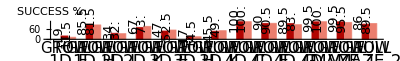

gpefs-grow-full-direct.pdf

```mathematica
parts = 2;
colNumber=2;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"1D","2D","3D","4D","M1","M2"}}];
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange,ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
Export["gpefs-grow-full-direct.pdf",cellS]
```

## Experiments Direct Best/Choice

```mathematica
names={"T/NEAT","T/GP","T/AT_G_OR_BEST","T/AT_G_OR_CHOICE","T/AT_G_GP_BEST","T/AT_G_GP_CHOICE","T/AT_G_NC_BEST","T/AT_G_NC_CHOICE","T/AT_B_OR_BEST","T/AT_B_OR_CHOICE","T/AT_B_NC_BEST","T/AT_B_NC_CHOICE","T/AT_B_GP_BEST","T/AT_B_GP_CHOICE","T/GP_GPEFS_GENERAL_BEST_GECCO","T/GP_GPEFS_GENERAL_CHOICE_GECCO"};
names={"T/NEAT","T/GP","T/AT_G_OR_BEST","T/AT_G_GP_BEST","T/AT_G_NC_BEST","T/AT_B_OR_BEST","T/AT_B_NC_BEST","T/AT_B_GP_BEST","T/AT_R","T/GP_GPEFS_GENERAL_BEST_GECCO"};
(*names={"T/NEAT","T/GP","T/AT_G_OR_CHOICE","T/AT_G_GP_CHOICE","T/AT_G_NC_CHOICE","T/AT_B_OR_CHOICE","T/AT_B_NC_CHOICE","T/AT_B_GP_CHOICE","T/AT_R","T/GP_GPEFS_GENERAL_CHOICE_GECCO"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
printAsTable[sortedData,{"SOLVER","ID","VARIANT","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TARGET_FITNESS,GP.TYPE,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SOLVER,SYMBOLIC_REGRESSION.F}

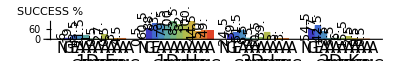

ALL_BEST_DIRECT_1D_2D.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"1D","2D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_CHOICE_DIRECT_1D_2D.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_BEST_DIRECT_1D_2D.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

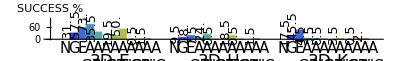

ALL_BEST_DIRECT_3D.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"3D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[5;;-1]],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems[[5;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems[[5;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems[[5;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_CHOICE_DIRECT_3D.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_BEST_DIRECT_3D.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

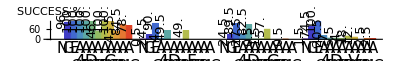

ALL_BEST_DIRECT_4D.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"4D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[8;;-1]],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems[[8;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems[[8;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems[[8;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_CHOICE_DIRECT_4D.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_BEST_DIRECT_4D.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

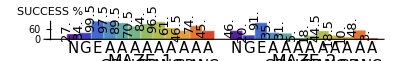

ALL_BEST_DIRECT_MAZE.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"M1","M2"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[12;;-1]],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems[[12;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems[[12;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems[[12;;-1]],2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_CHOICE_DIRECT_MAZE.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_BEST_DIRECT_MAZE.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Direct Aggregated Distance Choice

```mathematica
names={"T/AT_G_OR_CHOICE","T/AT_G_GP_CHOICE","T/AT_G_NC_CHOICE","T/AT_B_OR_CHOICE","T/AT_B_NC_CHOICE","T/AT_B_GP_CHOICE","T/AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,13]]];
printAsTable[aggregatedData,{"SOLVER","ID","VARIANT","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

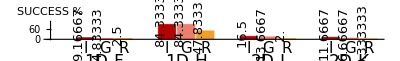

ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_1D_2D.pdf

```mathematica
parts = 3;
colNumber=3;
cellAll={};
problem={"1D","2D"};
aggregatedLabels=Flatten[Array[{"I","G","R"}&,13]];

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_1D_2D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

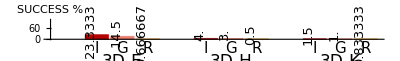

ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_3D.pdf

```mathematica
problem={"3D"};
listOfProblems=listOfDirectProblems[[5;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_3D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

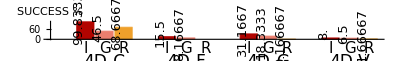

ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_4D.pdf

```mathematica
problem={"4D"};
listOfProblems=listOfDirectProblems[[8;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_4D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

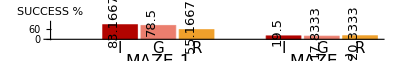

ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_MAZE.pdf

```mathematica
problem={"M1","M2"};
listOfProblems=listOfDirectProblems[[12;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_DIRECT_MAZE.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Direct Aggregated Implementation Choice

```mathematica
names={"T/AT_G_OR_CHOICE","T/AT_G_GP_CHOICE","T/AT_G_NC_CHOICE","T/AT_B_OR_CHOICE","T/AT_B_NC_CHOICE","T/AT_B_GP_CHOICE","T/AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.FUNCTION_IMPL","GPAT.DISTANCE","VARIANT"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,13]]];
printAsTable[aggregatedData,{"SOLVER","ID","VARIANT","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.TARGET_FITNESS,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SYMBOLIC_REGRESSION.F}

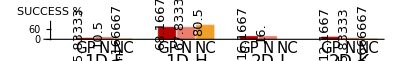

ALL_CHOICE_AGGREGATED_IMPL_DIRECT_1D_2D.pdf

```mathematica
parts = 3;
colNumber=3;
cellAll={};
problem={"1D","2D"};
aggregatedLabels=Flatten[Array[{"GP","N","NC"}&,13]];

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_DIRECT_1D_2D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

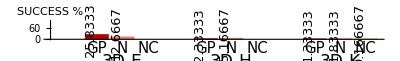

ALL_CHOICE_AGGREGATED_IMPL_DIRECT_3D.pdf

```mathematica
problem={"3D"};
listOfProblems=listOfDirectProblems[[5;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_DIRECT_3D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

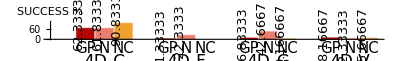

ALL_CHOICE_AGGREGATED_IMPL_DIRECT_4D.pdf

```mathematica
problem={"4D"};
listOfProblems=listOfDirectProblems[[8;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_DIRECT_4D.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

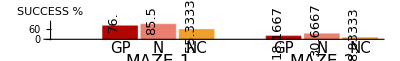

ALL_CHOICE_AGGREGATED_IMPL_DIRECT_MAZE.pdf

```mathematica
problem={"M1","M2"};
listOfProblems=listOfDirectProblems[[12;;-1]];
cellAll={};

aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,aggregatedLabels];
selectedData=selectData[aggregatedData,{"PROBLEM"->problem}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_DIRECT_MAZE.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Direct NEAT Only

```mathematica
names={"T/NEAT"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}];
printAsTable[sortedData,{"SOLVER","ID","VARIANT","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.TARGET_FITNESS,ID,MAZE.MAP,PROBLEM,SYMBOLIC_REGRESSION.F}

ID | PARAM FILE | SOLVER | ID | VARIANT | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | PROBLEM | SYMBOLIC_REGRESSION.F | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | MAZE.MAP
{N} | T/NEAT/parameters_001.txt | NEAT | 1D |  |  |  | 1D | F |  |  |  | 
{N} | T/NEAT/parameters_002.txt | NEAT | 1D |  |  |  | 1D | H |  |  |  | 
{N} | T/NEAT/parameters_003.txt | NEAT | 2D |  |  |  | 2D | I |  |  |  | 
{N} | T/NEAT/parameters_004.txt | NEAT | 2D |  |  |  | 2D | K |  |  |  | 
{N} | T/NEAT/parameters_005.txt | NEAT | 3D |  |  |  | 3D | E |  |  |  | 
{N} | T/NEAT/parameters_006.txt | NEAT | 3D |  |  |  | 3D | H |  |  |  | 
{N} | T/NEAT/parameters_007.txt | NEAT | 3D |  |  |  | 3D | K |  |  |  | 
{N} | T/NEAT/parameters_008.txt | NEAT | 4D |  |  |  | 4D | C |  |  |  | 
{N} | T/NEAT/parameters_009.txt | NEAT | 4D |  |  |  | 4D | F |  |  |  | 
{N} | T/NEAT/parameters_010.txt | NEAT | 4D |  |  |  | 4D | G |  |  |  | 
{N} | T/NEAT/parameters_011.txt | NEAT | 4D |  |  |  | 4D | V |  |  |  | 
{N} | T/NEAT/parameters_012.txt | NEAT | MAZE |  |  |  | M1 |  |  |  |  | map2.csv
{N} | T/NEAT/parameters_013.txt | NEAT | MAZE |  |  |  | M2 |  |  |  |  | map4.csv

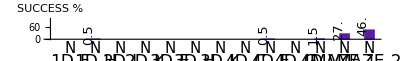

NEAT_DIRECT.pdf

```mathematica
parts = 1;
colNumber=13;
cellAll={};
selectedData=sortedData;
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN}}]}}];
Export["NEAT_DIRECT.pdf",Grid[{{Style["NEAT Direct: Success, Constants, Nodes",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments GPAT Indirect Innovation Numbers

```mathematica
names={"T/HAT_B_OR","T/HAT_B_NC","T/HAT_B_GP","T/HAT_B_ROBO","T/HAT_B_AC","T/HAT_B_AC_ROBO","T/HAT_B_CO","T/HAT_B_CO_ROBO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE_C1","GPAT.DISTANCE_C2","GPAT.DISTANCE_CACT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite,
distanceGeneralC1LabelRewrite,
distanceGeneralC2LabelRewrite,
distanceGeneralCACTLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","GPAT.DISTANCE_C1","GPAT.DISTANCE_C2","GPAT.DISTANCE_CACT","RECO.GENERATOR","PROBLEM"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS,STORE_GENOTYPES_MATHEMATICA}

```mathematica
parts = 81;
cellAll={};
colNumber->3;

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCM",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCS",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCR",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"XOR"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["XOR",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"FC"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["FC",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["ROBO",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

Export["AT_B_INDIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"",Style["GPAT Innovation Numbers: Success, Constants, Nodes, Depth",FontSize->25]},#},Frame->All]]&/@cellAll
```

{AT_B_INDIRECT_rCM.pdf,AT_B_INDIRECT_rCS.pdf,AT_B_INDIRECT_rCR.pdf,AT_B_INDIRECT_XOR.pdf,AT_B_INDIRECT_FC.pdf,AT_B_INDIRECT_ROBO.pdf}

```mathematica
parts = 27;
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
gridBIN=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBIN=Transpose[Transpose[gridBIN[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
gridBINC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBINC=Transpose[Transpose[gridBINC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
gridBIGP=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBIGP=Transpose[Transpose[gridBIGP[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"}}];
gridBIAC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBIAC=Transpose[Transpose[gridBIAC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"}}];
gridBICO=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridBICO=Transpose[Transpose[gridBICO[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
```

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
5 | 1. | 2. | 2. | 62.8333 | 103/12
26 | 5. | 5. | 2. | 63.6667 | 28/3
10 | 2. | 1. | 1. | 64.5833 | 29/3
14 | 2. | 2. | 2. | 63.3333 | 39/4
19 | 5. | 1. | 1. | 66.75 | 127/12
13 | 2. | 2. | 1. | 64.5 | 34/3
4 | 1. | 2. | 1. | 64.4167 | 37/3
1 | 1. | 1. | 1. | 64.8333 | 77/6
25 | 5. | 5. | 1. | 67.6667 | 79/6
8 | 1. | 5. | 2. | 64.75 | 79/6
16 | 2. | 5. | 1. | 65.4167 | 40/3
15 | 2. | 2. | 5. | 64.3333 | 167/12
23 | 5. | 2. | 2. | 66.9167 | 175/12
7 | 1. | 5. | 1. | 64.3333 | 89/6
22 | 5. | 2. | 1. | 68.25 | 31/2
18 | 2. | 5. | 5. | 65.9167 | 31/2
6 | 1. | 2. | 5. | 63.8333 | 31/2
27 | 5. | 5. | 5. | 66.75 | 187/12
20 | 5. | 1. | 2. | 67.8333 | 187/12
3 | 1. | 1. | 5. | 64.4167 | 187/12
11 | 2. | 1. | 2. | 65.0833 | 47/3
2 | 1. | 1. | 2. | 64.3333 | 193/12
24 | 5. | 2. | 5. | 65.8333 | 97/6
21 | 5. | 1. | 5. | 66.0833 | 97/6
9 | 1. | 5. | 5. | 65.8333 | 65/4
17 | 2. | 5. | 2. | 66.3333 | 37/2
12 | 2. | 1. | 5. | 64.9167 | 37/2

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
25 | 5. | 5. | 1. | 46.5 | 15/2
15 | 2. | 2. | 5. | 45.3333 | 25/3
16 | 2. | 5. | 1. | 47. | 32/3
13 | 2. | 2. | 1. | 46.9167 | 131/12
26 | 5. | 5. | 2. | 47.5833 | 67/6
7 | 1. | 5. | 1. | 48. | 71/6
10 | 2. | 1. | 1. | 48. | 143/12
23 | 5. | 2. | 2. | 47. | 151/12
6 | 1. | 2. | 5. | 47.75 | 151/12
11 | 2. | 1. | 2. | 47.9167 | 155/12
22 | 5. | 2. | 1. | 48.75 | 157/12
1 | 1. | 1. | 1. | 48.8333 | 40/3
27 | 5. | 5. | 5. | 49.25 | 14
3 | 1. | 1. | 5. | 48.5833 | 169/12
24 | 5. | 2. | 5. | 48.4167 | 85/6
20 | 5. | 1. | 2. | 48.5 | 29/2
14 | 2. | 2. | 2. | 48.6667 | 59/4
5 | 1. | 2. | 2. | 48.75 | 179/12
9 | 1. | 5. | 5. | 49.4167 | 191/12
4 | 1. | 2. | 1. | 49.8333 | 65/4
12 | 2. | 1. | 5. | 49.9167 | 49/3
2 | 1. | 1. | 2. | 49.1667 | 103/6
19 | 5. | 1. | 1. | 50.0833 | 209/12
8 | 1. | 5. | 2. | 49.9167 | 71/4
21 | 5. | 1. | 5. | 49.8333 | 107/6
18 | 2. | 5. | 5. | 50.3333 | 107/6
17 | 2. | 5. | 2. | 50.4167 | 73/4

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
3 | 1. | 1. | 5. | 43.5 | 29/6
6 | 1. | 2. | 5. | 47.5833 | 11/2
12 | 2. | 1. | 5. | 49.5 | 6
9 | 1. | 5. | 5. | 51.5 | 115/12
15 | 2. | 2. | 5. | 54. | 39/4
2 | 1. | 1. | 2. | 53.5 | 43/4
18 | 2. | 5. | 5. | 58. | 67/6
5 | 1. | 2. | 2. | 56.75 | 143/12
26 | 5. | 5. | 2. | 60.3333 | 53/4
8 | 1. | 5. | 2. | 58.1667 | 41/3
11 | 2. | 1. | 2. | 60.5833 | 83/6
16 | 2. | 5. | 1. | 60.6667 | 43/3
22 | 5. | 2. | 1. | 60.9167 | 89/6
7 | 1. | 5. | 1. | 59.3333 | 89/6
17 | 2. | 5. | 2. | 61.5833 | 15
24 | 5. | 2. | 5. | 61.75 | 47/3
21 | 5. | 1. | 5. | 60.75 | 95/6
19 | 5. | 1. | 1. | 61.8333 | 16
4 | 1. | 2. | 1. | 62. | 65/4
25 | 5. | 5. | 1. | 61.75 | 197/12
1 | 1. | 1. | 1. | 61.9167 | 33/2
13 | 2. | 2. | 1. | 63.3333 | 35/2
14 | 2. | 2. | 2. | 63.1667 | 53/3
27 | 5. | 5. | 5. | 62.75 | 217/12
10 | 2. | 1. | 1. | 63.25 | 229/12
20 | 5. | 1. | 2. | 66.8333 | 77/4
23 | 5. | 2. | 2. | 63.25 | 41/2

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
1 | 1. | 1. | 1. | 69.5833 | 23/4
3 | 1. | 1. | 5. | 72.6667 | 17/2
11 | 2. | 1. | 2. | 73.25 | 53/6
5 | 1. | 2. | 2. | 74. | 29/3
2 | 1. | 1. | 2. | 73.9167 | 121/12
10 | 2. | 1. | 1. | 72.5833 | 61/6
4 | 1. | 2. | 1. | 73.9167 | 11
13 | 2. | 2. | 1. | 73.3333 | 139/12
12 | 2. | 1. | 5. | 72.8333 | 143/12
15 | 2. | 2. | 5. | 75. | 13
9 | 1. | 5. | 5. | 75.25 | 13
14 | 2. | 2. | 2. | 75. | 27/2
23 | 5. | 2. | 2. | 74.25 | 41/3
21 | 5. | 1. | 5. | 75.5833 | 85/6
6 | 1. | 2. | 5. | 75.5 | 44/3
8 | 1. | 5. | 2. | 75.9167 | 179/12
18 | 2. | 5. | 5. | 75.1667 | 47/3
19 | 5. | 1. | 1. | 75.5833 | 97/6
24 | 5. | 2. | 5. | 75.5833 | 199/12
17 | 2. | 5. | 2. | 77.25 | 67/4
22 | 5. | 2. | 1. | 77.3333 | 103/6
20 | 5. | 1. | 2. | 75.6667 | 103/6
7 | 1. | 5. | 1. | 77.75 | 217/12
26 | 5. | 5. | 2. | 79.25 | 221/12
25 | 5. | 5. | 1. | 79.3333 | 56/3
16 | 2. | 5. | 1. | 77.4167 | 75/4
27 | 5. | 5. | 5. | 76.8333 | 121/6

ID | GPAT.DISTANCE_C1 | GPAT.DISTANCE_C2 | GPAT.DISTANCE_CACT | AVGS | RANK
6 | 1. | 2. | 5. | 12.5 | 131/12
11 | 2. | 1. | 2. | 13.3333 | 45/4
3 | 1. | 1. | 5. | 14.1667 | 35/3
2 | 1. | 1. | 2. | 14.1667 | 35/3
13 | 2. | 2. | 1. | 15. | 37/3
14 | 2. | 2. | 2. | 12.5833 | 13
24 | 5. | 2. | 5. | 13.4167 | 40/3
26 | 5. | 5. | 2. | 15.8333 | 41/3
23 | 5. | 2. | 2. | 15.8333 | 41/3
19 | 5. | 1. | 1. | 15.8333 | 41/3
18 | 2. | 5. | 5. | 15.8333 | 41/3
17 | 2. | 5. | 2. | 15.8333 | 41/3
8 | 1. | 5. | 2. | 15.8333 | 41/3
4 | 1. | 2. | 1. | 14.25 | 55/4
27 | 5. | 5. | 5. | 15.0833 | 173/12
22 | 5. | 2. | 1. | 15.0833 | 173/12
21 | 5. | 1. | 5. | 15.0833 | 173/12
12 | 2. | 1. | 5. | 15.0833 | 173/12
25 | 5. | 5. | 1. | 16.6667 | 179/12
16 | 2. | 5. | 1. | 16.6667 | 179/12
10 | 2. | 1. | 1. | 16.6667 | 179/12
7 | 1. | 5. | 1. | 16.6667 | 179/12
20 | 5. | 1. | 2. | 15.9167 | 63/4
9 | 1. | 5. | 5. | 15.9167 | 63/4
5 | 1. | 2. | 2. | 15.9167 | 63/4
15 | 2. | 2. | 5. | 16. | 67/4
1 | 1. | 1. | 1. | 16. | 67/4

For PLAIN GPAT choose (c1, c2, cACT) = (5, 2, 5) for both DIRECT/INDIRECT.

```mathematica
grid=Join[gridBDN,gridBIN];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(5. | 2. | 5. | 4.
2. | 1. | 2. | 4.5
1. | 1. | 2. | 5.
5. | 1. | 5. | 5.5
1. | 5. | 5. | 6.5
2. | 1. | 5. | 7.
2. | 5. | 2. | 7.
5. | 1. | 2. | 7.
1. | 1. | 5. | 8.
1. | 2. | 5. | 8.5
5. | 5. | 5. | 9.5
5. | 1. | 1. | 12.
5. | 2. | 2. | 13.
2. | 2. | 5. | 15.
5. | 2. | 1. | 15.5
1. | 5. | 2. | 16.5
1. | 1. | 1. | 18.
2. | 5. | 5. | 18.
5. | 5. | 1. | 18.
1. | 2. | 1. | 20.
2. | 5. | 1. | 20.
1. | 5. | 1. | 20.5
2. | 2. | 1. | 21.5
5. | 5. | 2. | 23.
2. | 1. | 1. | 23.5
2. | 2. | 2. | 24.5
1. | 2. | 2. | 26.5)

For NC GPAT choose (c1, c2, cACT) = (5, 1, 2) for both DIRECT/INDIRECT.

```mathematica
grid=Join[gridBDNC,gridBINC];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(5. | 1. | 5. | 2.
2. | 5. | 5. | 5.
5. | 2. | 5. | 8.
1. | 1. | 2. | 9.
1. | 2. | 2. | 9.5
5. | 1. | 2. | 9.5
2. | 1. | 2. | 10.
5. | 1. | 1. | 10.
5. | 5. | 5. | 10.5
1. | 2. | 1. | 12.5
2. | 1. | 1. | 12.5
1. | 5. | 2. | 13.
2. | 1. | 5. | 13.
2. | 5. | 2. | 13.
1. | 1. | 1. | 13.5
1. | 5. | 5. | 13.5
2. | 2. | 2. | 13.5
5. | 5. | 2. | 14.
5. | 2. | 2. | 15.
5. | 2. | 1. | 15.5
1. | 1. | 5. | 17.
2. | 2. | 5. | 19.5
1. | 2. | 5. | 22.5
1. | 5. | 1. | 22.5
2. | 2. | 1. | 24.
5. | 5. | 1. | 24.
2. | 5. | 1. | 26.)

For GP GPAT choose (c1, c2, cACT) = (5, 1, 2) for both DIRECT/INDIRECT.

```mathematica
grid=Join[gridBDGP,gridBIGP];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(5. | 1. | 2. | 1.5
2. | 1. | 1. | 4.
5. | 2. | 2. | 4.5
5. | 5. | 5. | 5.5
1. | 1. | 1. | 6.5
5. | 1. | 5. | 6.5
2. | 2. | 2. | 7.
5. | 1. | 1. | 7.
2. | 2. | 1. | 8.5
2. | 1. | 2. | 10.
1. | 2. | 1. | 12.
5. | 2. | 5. | 12.
5. | 2. | 1. | 12.5
2. | 5. | 2. | 13.
5. | 5. | 1. | 15.
1. | 5. | 2. | 16.
2. | 5. | 1. | 17.5
5. | 5. | 2. | 17.5
1. | 2. | 2. | 19.
1. | 5. | 1. | 19.
2. | 5. | 5. | 19.
1. | 1. | 2. | 21.5
2. | 2. | 5. | 21.5
2. | 1. | 5. | 24.
1. | 5. | 5. | 24.5
1. | 2. | 5. | 26.
1. | 1. | 5. | 27.)

For AC GPAT choose (c1, c2, cACT) = (5, 5, 5) for both DIRECT/INDIRECT.

```mathematica
grid=Join[gridBDAC,gridBIAC];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(5. | 5. | 5. | 4.5
5. | 1. | 2. | 5.5
5. | 2. | 5. | 5.5
5. | 1. | 1. | 7.
5. | 1. | 5. | 7.5
5. | 5. | 1. | 10.
2. | 2. | 2. | 11.5
2. | 2. | 5. | 12.
5. | 5. | 2. | 12.
1. | 2. | 5. | 13.
1. | 5. | 1. | 13.5
2. | 1. | 2. | 14.
2. | 5. | 1. | 14.5
2. | 5. | 5. | 15.
5. | 2. | 1. | 15.
2. | 5. | 2. | 16.
1. | 5. | 2. | 16.5
1. | 5. | 5. | 16.5
2. | 1. | 5. | 17.
1. | 1. | 2. | 17.5
1. | 2. | 2. | 17.5
1. | 1. | 1. | 18.
1. | 1. | 5. | 18.
2. | 1. | 1. | 18.
1. | 2. | 1. | 19.5
5. | 2. | 2. | 20.5
2. | 2. | 1. | 22.5)

For CO GPAT choose (c1, c2, cACT) = (5, 1, 2) for both DIRECT/INDIRECT.

```mathematica
grid=Join[gridBDCO,gridBICO];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(5. | 1. | 2. | 3.
2. | 1. | 1. | 5.
1. | 1. | 1. | 6.
5. | 1. | 5. | 8.5
1. | 2. | 1. | 10.5
5. | 2. | 2. | 10.5
5. | 1. | 1. | 11.5
1. | 2. | 2. | 12.
2. | 2. | 5. | 12.
1. | 5. | 1. | 12.5
2. | 5. | 2. | 12.5
5. | 2. | 1. | 12.5
5. | 5. | 5. | 12.5
5. | 5. | 1. | 13.
1. | 5. | 5. | 14.
2. | 5. | 1. | 14.
5. | 2. | 5. | 14.5
2. | 1. | 2. | 15.
1. | 5. | 2. | 15.5
2. | 2. | 2. | 16.
2. | 5. | 5. | 16.
2. | 1. | 5. | 16.5
5. | 5. | 2. | 17.
2. | 2. | 1. | 20.5
1. | 1. | 2. | 25.
1. | 1. | 5. | 26.
1. | 2. | 5. | 26.)

```mathematica
perm[x_]:=Permute[x,{1,2,3,4,6,5}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{2.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_B_OR_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_B_NC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{2.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_B_GP_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{5.},"GPAT.DISTANCE_CACT"->{5.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_B_AC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"},"GPAT.DISTANCE_C1"->{5.},"GPAT.DISTANCE_C2"->{1.},"GPAT.DISTANCE_CACT"->{2.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_B_CO_CHOICE"];
```

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_B_OR_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_B_NC_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_B_GP_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_B_AC_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_B_CO_BEST"];
```

## Experiments GPAT Indirect Generalized

```mathematica
names={"T/HAT_G_OR","T/HAT_G_NC","T/HAT_G_GP","T/HAT_G_ROBO","T/HAT_G_AC","T/HAT_G_AC_ROBO","T/HAT_G_CO","T/HAT_G_CO_ROBO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite,
distanceGeneralKLabelRewrite,
distanceGeneralAlphaLabelRewrite,
distanceGeneralBetaLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","RECO.GENERATOR","PROBLEM"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS,STORE_GENOTYPES_MATHEMATICA}

```mathematica
parts = 36;
colNumber=3;

cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCM",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCS",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["rCR",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"XOR"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["XOR",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"FC"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["FC55",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

selectedData=selectData[sortedData,{"PROBLEM"->{"ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",Array[#&,27],2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["ROBO",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];

Export["AT_G_INDIRECT_"<>#[[1,1]]<>".pdf",Grid[{{"",Style["GPAT Generalized: Success, Constants, Nodes, Depth",FontSize->25]},#},Frame->All]]&/@cellAll
```

{AT_G_INDIRECT_rCM.pdf,AT_G_INDIRECT_rCS.pdf,AT_G_INDIRECT_rCR.pdf,AT_G_INDIRECT_XOR.pdf,AT_G_INDIRECT_FC55.pdf,AT_G_INDIRECT_ROBO.pdf}

```mathematica
parts = 12;
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
gridGIN=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGIN=Transpose[Transpose[gridGIN[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
gridGIGP=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGIGP=Transpose[Transpose[gridGIGP[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
gridGINC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGINC=Transpose[Transpose[gridGINC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"}}];
gridGIAC=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGIAC=Transpose[Transpose[gridGIAC[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"}}];
gridGICO=printBooleanRanksAsTable[selectedData,"SUCCESS",parts]
gridGICO=Transpose[Transpose[gridGICO[[1,2;;All,2;;4]]]~Join~{Array[parts+1-#&,parts]}];
(*printAsTable[selectedData,changingParameters[data]]*)
```

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
11 | true | 10. | false | 33.3333 | 10/3
12 | true | 10. | true | 34.1667 | 23/6
10 | false | 10. | true | 38.8333 | 53/12
9 | false | 10. | false | 38.75 | 19/4
6 | false | 2. | true | 41.6667 | 67/12
5 | false | 2. | false | 48.1667 | 19/3
8 | true | 2. | true | 61.3333 | 41/6
2 | false | 1. | true | 46.3333 | 29/4
4 | true | 1. | true | 62.8333 | 31/4
7 | true | 2. | false | 62.8333 | 49/6
1 | false | 1. | false | 67.6667 | 37/4
3 | true | 1. | false | 72.4167 | 21/2

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
2 | false | 1. | true | 21.75 | 37/12
6 | false | 2. | true | 28.8333 | 29/6
9 | false | 10. | false | 30.8333 | 61/12
4 | true | 1. | true | 26.1667 | 21/4
1 | false | 1. | false | 29.4167 | 21/4
10 | false | 10. | true | 32.5833 | 73/12
12 | true | 10. | true | 33.25 | 13/2
11 | true | 10. | false | 32.4167 | 83/12
5 | false | 2. | false | 36.4167 | 91/12
8 | true | 2. | true | 36.25 | 8
7 | true | 2. | false | 48.9167 | 37/4
3 | true | 1. | false | 54. | 61/6

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
10 | false | 10. | true | 25.5833 | 35/12
12 | true | 10. | true | 27.3333 | 53/12
9 | false | 10. | false | 28.9167 | 9/2
11 | true | 10. | false | 27.9167 | 59/12
6 | false | 2. | true | 29.4167 | 23/4
2 | false | 1. | true | 32.25 | 6
8 | true | 2. | true | 42.3333 | 27/4
5 | false | 2. | false | 36.1667 | 29/4
1 | false | 1. | false | 42.9167 | 97/12
7 | true | 2. | false | 45. | 103/12
4 | true | 1. | true | 49.1667 | 109/12
3 | true | 1. | false | 45.5833 | 39/4

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
12 | true | 10. | true | 53.4167 | 25/6
9 | false | 10. | false | 53.5 | 9/2
11 | true | 10. | false | 55.4167 | 59/12
10 | false | 10. | true | 54.9167 | 61/12
6 | false | 2. | true | 57. | 61/12
2 | false | 1. | true | 63.0833 | 35/6
8 | true | 2. | true | 69.5833 | 27/4
5 | false | 2. | false | 66.3333 | 43/6
4 | true | 1. | true | 74.8333 | 15/2
1 | false | 1. | false | 67.8333 | 23/3
7 | true | 2. | false | 76.9167 | 107/12
3 | true | 1. | false | 80.5 | 125/12

ID | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
6 | false | 2. | true | 15. | 11/2
1 | false | 1. | false | 15. | 11/2
11 | true | 10. | false | 15.8333 | 73/12
10 | false | 10. | true | 15.8333 | 73/12
4 | true | 1. | true | 15.8333 | 73/12
12 | true | 10. | true | 16.6667 | 83/12
9 | false | 10. | false | 16.6667 | 83/12
8 | true | 2. | true | 16.6667 | 83/12
7 | true | 2. | false | 16.6667 | 83/12
5 | false | 2. | false | 16.6667 | 83/12
2 | false | 1. | true | 15.9167 | 7
3 | true | 1. | false | 16. | 43/6

For PLAIN GPAT choose false, 1, false for both DIRECT/INDIRECT, i.e. (K, alpha, beta) = (1,0,0). Note, the order in the table is (beta, K, alpha).

```mathematica
grid=Join[gridGDN,gridGIN];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(false | 1. | false | 2.
false | 1. | true | 3.
true | 1. | false | 3.5
true | 1. | true | 3.5
false | 2. | false | 6.
false | 2. | true | 6.
true | 2. | false | 6.5
true | 2. | true | 7.5
false | 10. | false | 8.
false | 10. | true | 9.
true | 10. | true | 11.
true | 10. | false | 12.)

For GP GPAT choose true, 2, false for both DIRECT/INDIRECT, i.e. (K, alpha, beta) = (1,0,1).

```mathematica
grid=Join[gridGDGP,gridGIGP];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(true | 1. | false | 1.5
true | 2. | false | 1.5
true | 2. | true | 3.
true | 10. | false | 5.
false | 2. | false | 6.
true | 1. | true | 6.5
true | 10. | true | 6.5
false | 2. | true | 8.5
false | 10. | true | 9.
false | 10. | false | 9.5
false | 1. | false | 10.
false | 1. | true | 11.)

For No Consts GPAT choose true, 2, false for both DIRECT/INDIRECT, i.e. (K, alpha, beta) = (1,1,1).

```mathematica
grid=Join[gridGDNC,gridGINC];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(true | 1. | true | 1.5
true | 1. | false | 2.5
false | 1. | true | 4.5
true | 2. | true | 4.5
true | 2. | false | 5.
false | 2. | false | 6.5
false | 1. | false | 7.
false | 10. | false | 7.5
false | 10. | true | 9.
true | 10. | false | 9.
false | 2. | true | 10.
true | 10. | true | 11.)

For AC GPAT choose true, 2, false for both DIRECT/INDIRECT, i.e. (K, alpha, beta) = (1,0,0).

```mathematica
grid=Join[gridGDAC,gridGIAC];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(false | 1. | false | 2.
true | 1. | false | 3.
true | 1. | true | 3.5
false | 1. | true | 4.5
false | 2. | false | 4.5
true | 2. | false | 6.
true | 2. | true | 6.5
false | 2. | true | 7.
false | 10. | true | 9.
false | 10. | false | 9.5
true | 10. | false | 10.5
true | 10. | true | 12.)

For CO GPAT choose true, 2, false for both DIRECT/INDIRECT, i.e. (K, alpha, beta) = (1,0,1).

```mathematica
grid=Join[gridGDCO,gridGICO];
SortBy[Mean/@GatherBy[grid,#[[1;;3]]&],#[[4]]&]//N//MatrixForm
```

(true | 1. | false | 1.
true | 2. | false | 3.
true | 2. | true | 4.
false | 1. | true | 4.5
true | 1. | true | 6.
true | 10. | true | 6.5
false | 2. | false | 7.
true | 10. | false | 7.5
false | 10. | false | 9.
false | 10. | true | 9.5
false | 1. | false | 10.
false | 2. | true | 10.)

```mathematica
perm[x_]:=Permute[x,{1,2,3,4,6,5}];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"false"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_G_OR_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_G_GP_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"true"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_G_NC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"false"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_G_AC_CHOICE"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"},"GP.DISTANCE_GENERAL_K"->{1.},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"}}];
printAsTable[selectedData,changingParameters[data]];
saveData[perm[selectedData],"HAT_G_CO_CHOICE"];
```

```mathematica
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"N"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_G_OR_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"NC"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_G_NC_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"GP"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_G_GP_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"AC"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_G_AC_BEST"];
selectedData=selectData[sortedData,{"GPAT.FUNCTION_IMPL"->{"CO"}}];
printAsTable[selectedData,changingParameters[data]];
selectedData=selectMaximum[#,"SUCCESS"]&/@Partition[selectedData,parts];
saveData[perm[selectedData],"HAT_G_CO_BEST"];
```

## Experiments GPAT Indirect Random

```mathematica
names={"T/HAT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
functionImplLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=Flatten[Permute[Partition[sortedData,3],{2,4,3,6,1,5}],1];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","RECO.GENERATOR"}]
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE}

ID | PARAM FILE | SOLVER | ID | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | PROBLEM | SYMBOLIC_REGRESSION.F | RECO.GENERATOR
{GP} | T/HAT_R/parameters_003.txt | GPAT | RECO1D | RANDOM | GP | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D
{N} | T/HAT_R/parameters_001.txt | GPAT | RECO1D | RANDOM | N | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D
{NC} | T/HAT_R/parameters_002.txt | GPAT | RECO1D | RANDOM | NC | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D
{GP} | T/HAT_R/parameters_006.txt | GPAT | RECO1D | RANDOM | GP | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D
{N} | T/HAT_R/parameters_004.txt | GPAT | RECO1D | RANDOM | N | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D
{NC} | T/HAT_R/parameters_005.txt | GPAT | RECO1D | RANDOM | NC | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D
{GP} | T/HAT_R/parameters_009.txt | GPAT | RECO1D | RANDOM | GP | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D
{N} | T/HAT_R/parameters_007.txt | GPAT | RECO1D | RANDOM | N | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D
{NC} | T/HAT_R/parameters_008.txt | GPAT | RECO1D | RANDOM | NC | RECO |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D
{GP} | T/HAT_R/parameters_015.txt | GPAT | XOR | RANDOM | GP | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR
{N} | T/HAT_R/parameters_013.txt | GPAT | XOR | RANDOM | N | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR
{NC} | T/HAT_R/parameters_014.txt | GPAT | XOR | RANDOM | NC | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR
{GP} | T/HAT_R/parameters_012.txt | GPAT | FC | RANDOM | GP | FC |  | 
{N} | T/HAT_R/parameters_010.txt | GPAT | FC | RANDOM | N | FC |  | 
{NC} | T/HAT_R/parameters_011.txt | GPAT | FC | RANDOM | NC | FC |  | 
{GP} | T/HAT_R/parameters_018.txt | GPAT | ROBO | RANDOM | GP | ROBOTS |  | 
{N} | T/HAT_R/parameters_016.txt | GPAT | ROBO | RANDOM | N | ROBOTS |  | 
{NC} | T/HAT_R/parameters_017.txt | GPAT | ROBO | RANDOM | NC | ROBOTS |  |

```mathematica
parts = 3;
colNumber=3;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["AT_R_INDIRECT.pdf",Grid[{{Style["GPAT Random Indirect: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

AT_R_INDIRECT.pdf

```mathematica
printBooleanRanksAsTable[selectedData,"SUCCESS",3]
```

ID | GPAT.FUNCTION_IMPL | RANK
3 | NC | 13/10
1 | GP | 19/10
2 | N | 14/5

## Experiments GPEFS Indirect Generalized

```mathematica
names={"T/HGP_GPEFS_GENERAL_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC",("PARALLEL.FORCE_THREADS"->_)->("PARALLEL.FORCE_THREADS"->1)}];
epilog={Text[Style[Grid[{{"C"},{"α"},{"β"}},Spacings->{2,0}],Bold,FontSize->15],{0.7,-12}]};
padding={{30,0},{75,30}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","RECO.GENERATOR","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
{"GP.DISTANCE_GENERAL_C",{"."->""}},
{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"false"->"0","true"->"1"}},
{"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"false"->"0","true"->"1"}}
}];
sortedData=replaceLabels[sortedData,newLabels];
changingParameters[data]
printAsTable[sortedData,changingParameters[data]~Complement~{"GPAT.DISTANCE_PHENO_HIGH","GPAT.DISTANCE_PHENO_LOW","GPAT.DISTANCE_PHENO_STEPS","PARALLEL.FORCE_THREADS","GP.TARGET_FITNESS"}];
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.DISTANCE_GENERAL_C,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,ID,NET_ACTIVATIONS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE}

```mathematica
parts = 24;
gridEFSGI=printBooleanRanksAsTable[sortedData,"SUCCESS",parts]
gridEFSGI=Transpose[Transpose[gridEFSGI[[1,2;;All,2;;5]]]~Join~{Array[parts+1-#&,parts]}];
```

ID | GP.DISTANCE_GENERAL_C | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | AVGS | RANK
24 | 1. | true | 10. | true | 50.9 | 9
4 | 1. | false | 1. | true | 47.3 | 91/10
7 | 0. | true | 1. | true | 48.2 | 47/5
18 | 1. | false | 10. | false | 50.8 | 19/2
22 | 1. | true | 10. | false | 49.9 | 48/5
3 | 0. | false | 1. | true | 48. | 99/10
2 | 1. | false | 1. | false | 49.9 | 51/5
20 | 1. | false | 10. | true | 52.9 | 54/5
8 | 1. | true | 1. | true | 49.3 | 58/5
23 | 0. | true | 10. | true | 52.4 | 61/5
15 | 0. | true | 2. | true | 51.9 | 61/5
21 | 0. | true | 10. | false | 53. | 123/10
12 | 1. | false | 2. | true | 55.1 | 64/5
17 | 0. | false | 10. | false | 53.1 | 129/10
6 | 1. | true | 1. | false | 52.9 | 13
1 | 0. | false | 1. | false | 51.6 | 13
13 | 0. | true | 2. | false | 53.6 | 133/10
16 | 1. | true | 2. | true | 52.5 | 69/5
11 | 0. | false | 2. | true | 52.9 | 147/10
14 | 1. | true | 2. | false | 54.8 | 149/10
5 | 0. | true | 1. | false | 54. | 151/10
19 | 0. | false | 10. | true | 54. | 153/10
9 | 0. | false | 2. | false | 56.8 | 88/5
10 | 1. | false | 2. | false | 56.7 | 89/5

For GPEFS choose 0, true, 1, false for both DIRECT/INDIRECT, i.e. (alpha, beta, C, K) = (0,1,0,1).

```mathematica
grid=Join[gridEFSGD,gridEFSGI];
SortBy[Mean/@GatherBy[grid,#[[1;;4]]&],#[[5]]&]//N//MatrixForm
```

(0. | true | 1. | false | 2.5
0. | false | 2. | false | 3.5
1. | true | 2. | false | 5.5
1. | true | 1. | false | 6.
0. | false | 1. | false | 6.5
0. | true | 2. | false | 7.5
1. | false | 2. | false | 7.5
0. | false | 2. | true | 9.
0. | false | 10. | true | 10.5
1. | false | 1. | false | 10.5
1. | true | 1. | true | 12.5
0. | false | 1. | true | 13.5
0. | true | 2. | true | 13.5
1. | true | 2. | true | 13.5
0. | false | 10. | false | 14.
0. | true | 10. | false | 14.
0. | true | 10. | true | 15.5
1. | false | 2. | true | 15.5
0. | true | 1. | true | 16.5
1. | false | 1. | true | 16.5
1. | false | 10. | true | 19.
1. | true | 10. | false | 21.
1. | false | 10. | false | 22.
1. | true | 10. | true | 24.)

```mathematica
selectedData=selectData[sortedData,{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"->{"false"},"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"->{"true"},"GP.DISTANCE_GENERAL_C"->{0.},"GP.DISTANCE_GENERAL_K"->{1.}}];
printAsTable[selectedData,changingParameters[data]];
saveData[selectedData,"HGP_GPEFS_GENERAL_CHOICE_GECCO"];
```

## Full/Grow GPEFS Indirect

```mathematica
names={"T/HGP_GPEFS_GENERAL_CHOICE_GECCO","T/HGPEFS_FULL_G_CHOICE"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
data = removeData[data,{"PROBLEM"->{"ROBOTS"}}];
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
"GP.FULL_INIT"->{"true"->"FULL","false"->"GROW"}
}];
sortedData=replaceLabels[sortedData,newLabels];
sortedData=Flatten[Permute[Partition[sortedData,2],{2,4,3,5,1}],1];
printAsTable[sortedData,{"SOLVER","GP.TYPE","ID","GP.FULL_INIT","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.FULL_INIT,ID,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS}

ID | PARAM FILE | SOLVER | GP.TYPE | ID | GP.FULL_INIT | VARIANT | PROBLEM | RECO.GENERATOR | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT
{GROW} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_002.txt | GP | gp.GPEFS | RECO1D | false | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 1. | true | false
{FULL} | T/HGPEFS_FULL_G_CHOICE/parameters_001.txt | GP | gp.GPEFS | RECO1D | true | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 1. | true | false
{GROW} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_004.txt | GP | gp.GPEFS | RECO1D | false | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 1. | true | false
{FULL} | T/HGPEFS_FULL_G_CHOICE/parameters_002.txt | GP | gp.GPEFS | RECO1D | true | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 1. | true | false
{GROW} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_003.txt | GP | gp.GPEFS | RECO1D | false | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 1. | true | false
{FULL} | T/HGPEFS_FULL_G_CHOICE/parameters_003.txt | GP | gp.GPEFS | RECO1D | true | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 1. | true | false
{GROW} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_005.txt | GP | gp.GPEFS | XOR | false | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | 1. | true | false
{FULL} | T/HGPEFS_FULL_G_CHOICE/parameters_005.txt | GP | gp.GPEFS | XOR | true | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | 1. | true | false
{GROW} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_001.txt | GP | gp.GPEFS | FC | false | CHOICE | FC |  | 1. | true | false
{FULL} | T/HGPEFS_FULL_G_CHOICE/parameters_004.txt | GP | gp.GPEFS | FC | true | CHOICE | FC |  | 1. | true | false

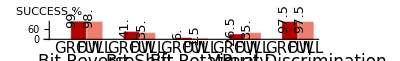

gpefs-grow-full-indirect.pdf

```mathematica
parts = 2;
colNumber=2;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"FC","RECO","XOR"}}];
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,0.1,parts,PlotRange->plotRange,ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
Export["gpefs-grow-full-indirect.pdf",cellS]
```

## Experiments Indirect Best/Choice

```mathematica
names={"T/HNEAT","T/HGP","T/HAT_G_OR_BEST","T/HAT_G_OR_CHOICE","T/HAT_G_GP_BEST","T/HAT_G_GP_CHOICE","T/HAT_G_NC_BEST","T/HAT_G_NC_CHOICE","T/HAT_B_OR_BEST","T/HAT_B_OR_CHOICE","T/HAT_B_GP_BEST","T/HAT_B_GP_CHOICE","T/HGP_GPEFS_GENERAL_BEST_GECCO","T/HGP_GPEFS_GENERAL_CHOICE_GECCO"};
(*names={"T/HNEAT","T/HGP","T/HAT_G_OR_BEST","T/HAT_G_GP_BEST","T/HAT_G_NC_BEST","T/HAT_B_OR_BEST","T/HAT_B_NC_BEST","T/HAT_B_GP_BEST","T/HAT_R","T/HGP_GPEFS_GENERAL_BEST_GECCO"};*)
names={"T/HNEAT","T/HGP","T/HAT_G_OR_CHOICE","T/HAT_G_GP_CHOICE","T/HAT_G_NC_CHOICE","T/HAT_B_OR_CHOICE","T/HAT_B_NC_CHOICE","T/HAT_B_GP_CHOICE","T/HAT_R","T/HGP_GPEFS_GENERAL_CHOICE_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=Flatten[Permute[Partition[sortedData,12],{2,4,3,6,1,5}],1];
printAsTable[sortedData,{"SOLVER","GP.TYPE","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}]
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_EVALUATIONS,GP.MAX_GENERATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.MUTATION_SUBTREE_PROBABLITY,GP.TARGET_FITNESS,GP.TYPE,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finished,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.generation,PRINT.progress,PRINT.storeRun,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS,SOLVER}

ID | PARAM FILE | SOLVER | GP.TYPE | ID | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | VARIANT | PROBLEM | RECO.GENERATOR | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT
{N} | T/HNEAT/parameters_001.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{G} | T/HGP/parameters_002.txt | GP | gp.GP | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{E} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_002.txt | GP | gp.GPEFS | RECO1D |  |  | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 1. | true | false
{A,GP,I} | T/HAT_B_GP_CHOICE/parameters_002.txt | GPAT | gpat.GPAT | RECO1D | BASIC | GP | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{A,N,I} | T/HAT_B_OR_CHOICE/parameters_002.txt | GPAT | gpat.GPAT | RECO1D | BASIC | N | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{A,NC,I} | T/HAT_B_NC_CHOICE/parameters_002.txt | GPAT | gpat.GPAT | RECO1D | BASIC | NC | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 10. | true | true
{A,GP,G} | T/HAT_G_GP_CHOICE/parameters_002.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | GP | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 2. | true | false
{A,N,G} | T/HAT_G_OR_CHOICE/parameters_002.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | N | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 1. | false | false
{A,NC,G} | T/HAT_G_NC_CHOICE/parameters_002.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | NC | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 1. | true | true
{A,GP,R} | T/HAT_R/parameters_003.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | GP |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{A,N,R} | T/HAT_R/parameters_001.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | N |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{A,NC,R} | T/HAT_R/parameters_002.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | NC |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{N} | T/HNEAT/parameters_002.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{G} | T/HGP/parameters_003.txt | GP | gp.GP | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{E} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_004.txt | GP | gp.GPEFS | RECO1D |  |  | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 1. | true | false
{A,GP,I} | T/HAT_B_GP_CHOICE/parameters_004.txt | GPAT | gpat.GPAT | RECO1D | BASIC | GP | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{A,N,I} | T/HAT_B_OR_CHOICE/parameters_004.txt | GPAT | gpat.GPAT | RECO1D | BASIC | N | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{A,NC,I} | T/HAT_B_NC_CHOICE/parameters_004.txt | GPAT | gpat.GPAT | RECO1D | BASIC | NC | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 10. | true | true
{A,GP,G} | T/HAT_G_GP_CHOICE/parameters_003.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | GP | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 2. | true | false
{A,N,G} | T/HAT_G_OR_CHOICE/parameters_003.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | N | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 1. | false | false
{A,NC,G} | T/HAT_G_NC_CHOICE/parameters_003.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | NC | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 1. | true | true
{A,GP,R} | T/HAT_R/parameters_006.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | GP |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{A,N,R} | T/HAT_R/parameters_004.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | N |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{A,NC,R} | T/HAT_R/parameters_005.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | NC |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{N} | T/HNEAT/parameters_003.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{G} | T/HGP/parameters_004.txt | GP | gp.GP | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{E} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_003.txt | GP | gp.GPEFS | RECO1D |  |  | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 1. | true | false
{A,GP,I} | T/HAT_B_GP_CHOICE/parameters_003.txt | GPAT | gpat.GPAT | RECO1D | BASIC | GP | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{A,N,I} | T/HAT_B_OR_CHOICE/parameters_003.txt | GPAT | gpat.GPAT | RECO1D | BASIC | N | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{A,NC,I} | T/HAT_B_NC_CHOICE/parameters_003.txt | GPAT | gpat.GPAT | RECO1D | BASIC | NC | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 10. | true | true
{A,GP,G} | T/HAT_G_GP_CHOICE/parameters_004.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | GP | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 2. | true | false
{A,N,G} | T/HAT_G_OR_CHOICE/parameters_004.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | N | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 1. | false | false
{A,NC,G} | T/HAT_G_NC_CHOICE/parameters_004.txt | GPAT | gpat.GPAT | RECO1D | GENERAL | NC | CHOICE | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 1. | true | true
{A,GP,R} | T/HAT_R/parameters_009.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | GP |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{A,N,R} | T/HAT_R/parameters_007.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | N |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{A,NC,R} | T/HAT_R/parameters_008.txt | GPAT | gpat.GPAT | RECO1D | RANDOM | NC |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{N} | T/HNEAT/parameters_005.txt | NEAT |  | XOR |  |  |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{G} | T/HGP/parameters_005.txt | GP | gp.GP | XOR |  |  |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{E} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_005.txt | GP | gp.GPEFS | XOR |  |  | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | 1. | true | false
{A,GP,I} | T/HAT_B_GP_CHOICE/parameters_005.txt | GPAT | gpat.GPAT | XOR | BASIC | GP | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{A,N,I} | T/HAT_B_OR_CHOICE/parameters_005.txt | GPAT | gpat.GPAT | XOR | BASIC | N | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{A,NC,I} | T/HAT_B_NC_CHOICE/parameters_005.txt | GPAT | gpat.GPAT | XOR | BASIC | NC | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | 10. | true | true
{A,GP,G} | T/HAT_G_GP_CHOICE/parameters_005.txt | GPAT | gpat.GPAT | XOR | GENERAL | GP | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | 2. | true | false
{A,N,G} | T/HAT_G_OR_CHOICE/parameters_005.txt | GPAT | gpat.GPAT | XOR | GENERAL | N | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | 1. | false | false
{A,NC,G} | T/HAT_G_NC_CHOICE/parameters_005.txt | GPAT | gpat.GPAT | XOR | GENERAL | NC | CHOICE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | 1. | true | true
{A,GP,R} | T/HAT_R/parameters_015.txt | GPAT | gpat.GPAT | XOR | RANDOM | GP |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{A,N,R} | T/HAT_R/parameters_013.txt | GPAT | gpat.GPAT | XOR | RANDOM | N |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{A,NC,R} | T/HAT_R/parameters_014.txt | GPAT | gpat.GPAT | XOR | RANDOM | NC |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{N} | T/HNEAT/parameters_004.txt | NEAT |  | FC |  |  |  | FC |  |  |  | 
{G} | T/HGP/parameters_001.txt | GP | gp.GP | FC |  |  |  | FC |  |  |  | 
{E} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_001.txt | GP | gp.GPEFS | FC |  |  | CHOICE | FC |  | 1. | true | false
{A,GP,I} | T/HAT_B_GP_CHOICE/parameters_001.txt | GPAT | gpat.GPAT | FC | BASIC | GP | CHOICE | FC |  |  |  | 
{A,N,I} | T/HAT_B_OR_CHOICE/parameters_001.txt | GPAT | gpat.GPAT | FC | BASIC | N | CHOICE | FC |  |  |  | 
{A,NC,I} | T/HAT_B_NC_CHOICE/parameters_001.txt | GPAT | gpat.GPAT | FC | BASIC | NC | CHOICE | FC |  | 10. | true | true
{A,GP,G} | T/HAT_G_GP_CHOICE/parameters_001.txt | GPAT | gpat.GPAT | FC | GENERAL | GP | CHOICE | FC |  | 2. | true | false
{A,N,G} | T/HAT_G_OR_CHOICE/parameters_001.txt | GPAT | gpat.GPAT | FC | GENERAL | N | CHOICE | FC |  | 1. | false | false
{A,NC,G} | T/HAT_G_NC_CHOICE/parameters_001.txt | GPAT | gpat.GPAT | FC | GENERAL | NC | CHOICE | FC |  | 1. | true | true
{A,GP,R} | T/HAT_R/parameters_012.txt | GPAT | gpat.GPAT | FC | RANDOM | GP |  | FC |  |  |  | 
{A,N,R} | T/HAT_R/parameters_010.txt | GPAT | gpat.GPAT | FC | RANDOM | N |  | FC |  |  |  | 
{A,NC,R} | T/HAT_R/parameters_011.txt | GPAT | gpat.GPAT | FC | RANDOM | NC |  | FC |  |  |  | 
{N} | T/HNEAT/parameters_006.txt | NEAT |  | ROBO |  |  |  | ROBOTS |  |  |  | 
{G} | T/HGP/parameters_006.txt | GP | gp.GP | ROBO |  |  |  | ROBOTS |  |  |  | 
{E} | T/HGP_GPEFS_GENERAL_CHOICE_GECCO/parameters_006.txt | GP | gp.GPEFS | ROBO |  |  | CHOICE | ROBOTS |  | 1. | true | false
{A,GP,I} | T/HAT_B_GP_CHOICE/parameters_006.txt | GPAT | gpat.GPAT | ROBO | BASIC | GP | CHOICE | ROBOTS |  |  |  | 
{A,N,I} | T/HAT_B_OR_CHOICE/parameters_006.txt | GPAT | gpat.GPAT | ROBO | BASIC | N | CHOICE | ROBOTS |  |  |  | 
{A,NC,I} | T/HAT_B_NC_CHOICE/parameters_006.txt | GPAT | gpat.GPAT | ROBO | BASIC | NC | CHOICE | ROBOTS |  |  |  | 
{A,GP,G} | T/HAT_G_GP_CHOICE/parameters_006.txt | GPAT | gpat.GPAT | ROBO | GENERAL | GP | CHOICE | ROBOTS |  | 2. | true | false
{A,N,G} | T/HAT_G_OR_CHOICE/parameters_006.txt | GPAT | gpat.GPAT | ROBO | GENERAL | N | CHOICE | ROBOTS |  | 1. | false | false
{A,NC,G} | T/HAT_G_NC_CHOICE/parameters_006.txt | GPAT | gpat.GPAT | ROBO | GENERAL | NC | CHOICE | ROBOTS |  | 1. | true | true
{A,GP,R} | T/HAT_R/parameters_018.txt | GPAT | gpat.GPAT | ROBO | RANDOM | GP |  | ROBOTS |  |  |  | 
{A,N,R} | T/HAT_R/parameters_016.txt | GPAT | gpat.GPAT | ROBO | RANDOM | N |  | ROBOTS |  |  |  | 
{A,NC,R} | T/HAT_R/parameters_017.txt | GPAT | gpat.GPAT | ROBO | RANDOM | NC |  | ROBOTS |  |  |  |

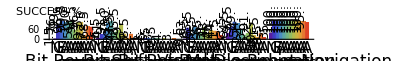

ALL_CHOICE_INDIRECT.pdf

```mathematica
parts = 12;
colNumber=12;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
(*Export["ALL_BEST_INDIRECT.pdf",Grid[{{Style["GPAT BEST: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]*)
Export["ALL_CHOICE_INDIRECT.pdf",Grid[{{Style["GPAT CHOICE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

```mathematica
printBooleanRanksAsTable[selectedData,"SUCCESS",3]
```

ID | GP.MUTATION_CAUCHY_PROBABILITY | GP.MUTATION_SUBTREE_PROBABLITY | GP.TYPE | PARALLEL.FORCE_THREADS | PRINT.finishedShowHyperNet | PRINT.finishedShowProblem | RECO.PATTERNS | SOLVER | AVGS | RANK
1 |  |  |  | 3 | false | false | 101; 110 | NEAT | 41.4167 | 83/48
3 | 0.1 | 0.8 | gp.GPEFS | 4 | true | true | 110 | GP | 48.3125 | 89/48
2 | 0.8 | 1. | gp.GP |  | true | true | 110 | GP | 58.8542 | 29/12

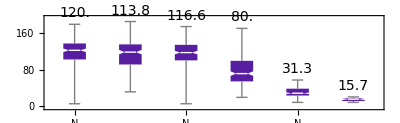

```mathematica
plotAsBoxWhiskerChartPub[selectData[sortedData,{"SOLVER"->{"NEAT"}}],"CONSTANTS_BSF",listOfDirectProblems,2.0,1,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]
```

## Experiments Indirect Aggregated Distance Choice

```mathematica
names={"T/HAT_G_OR_CHOICE","T/HAT_G_GP_CHOICE","T/HAT_G_NC_CHOICE","T/HAT_B_OR_CHOICE","T/HAT_B_NC_CHOICE","T/HAT_B_GP_CHOICE","T/HAT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=Flatten[Permute[Partition[sortedData,9],{2,4,3,6,1,5}],1];
aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,6]]];
printAsTable[aggregatedData,{"SOLVER","GP.TYPE","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS}

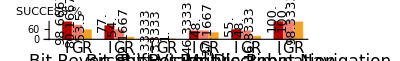

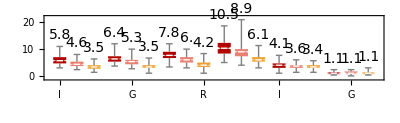

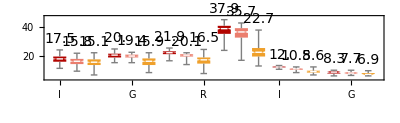

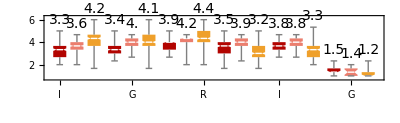

ALL_CHOICE_AGGREGATED_DISTANCE_INDIRECT.pdf

```mathematica
parts = 3;
colNumber=3;
cellAll={};

selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"I","G","R"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_DISTANCE_INDIRECT.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Indirect Aggregated Implementation Choice

```mathematica
names={"T/HAT_G_OR_CHOICE","T/HAT_G_GP_CHOICE","T/HAT_G_NC_CHOICE","T/HAT_B_OR_CHOICE","T/HAT_B_NC_CHOICE","T/HAT_B_GP_CHOICE","T/HAT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.FUNCTION_IMPL","GPAT.DISTANCE","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=Flatten[Permute[Partition[sortedData,9],{2,4,3,6,1,5}],1];
aggregatedData=aggregateBoolean[sortedData,"SUCCESS",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"GP","N","NC"}&,6]]];
printAsTable[aggregatedData,{"SOLVER","GP.TYPE","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE,GPAT.DISTANCE_C1,GPAT.DISTANCE_C2,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progress,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,RECO.PATTERNS}

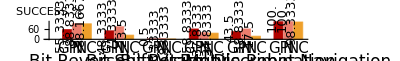

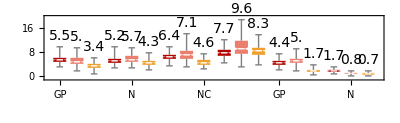

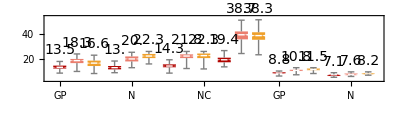

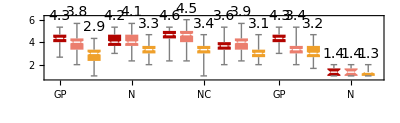

ALL_CHOICE_AGGREGATED_IMPL_INDIRECT.pdf

```mathematica
parts = 3;
colNumber=3;
cellAll={};

selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"CONSTANTS_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"GP","N","NC"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"NODES_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"GP","N","NC"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]

aggregatedData=aggregateBoolean[sortedData,"DEPTH_BSF",3];
aggregatedData=replaceLabels[aggregatedData,Flatten[Array[{"GP","N","NC"}&,6]]];
selectedData=selectData[aggregatedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfIndirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber]
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["ALL_CHOICE_AGGREGATED_IMPL_INDIRECT.pdf",Grid[{{Style["GPAT CHOICE AGGREGATED DISTANCE: Success, Constants, Nodes, Depth",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

## Experiments Indirect NEAT Only

```mathematica
names={"T/HNEAT"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GPAT.FUNCTION_IMPL"}];
newLabels=extractParameters[sortedData,{
solverLabelRewrite,
functionImplLabelRewrite,
distanceLabelRewrite,
{"GP.TYPE",{}}
}];
newLabels=newLabels/.{{"G",___,"gp.GP"}->{"G"},{"G",___,"gp.GPEFS"}->{"E"},{"N",___}->{"N"},{"AT",none:__,"gpat.GPAT"}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
sortedData=Flatten[Permute[Partition[sortedData,1],{2,4,3,6,1,5}],1];
printAsTable[sortedData,{"SOLVER","GP.TYPE","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","VARIANT","PROBLEM","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}]
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.MAX_GENERATIONS,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE}

ID | PARAM FILE | SOLVER | GP.TYPE | ID | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | VARIANT | PROBLEM | RECO.GENERATOR | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT
{N} | T/HNEAT/parameters_001.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D |  |  | 
{N} | T/HNEAT/parameters_002.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D |  |  | 
{N} | T/HNEAT/parameters_003.txt | NEAT |  | RECO1D |  |  |  | RECO | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D |  |  | 
{N} | T/HNEAT/parameters_005.txt | NEAT |  | XOR |  |  |  | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR |  |  | 
{N} | T/HNEAT/parameters_004.txt | NEAT |  | FC |  |  |  | FC |  |  |  | 
{N} | T/HNEAT/parameters_006.txt | NEAT |  | ROBO |  |  |  | ROBOTS |  |  |  |

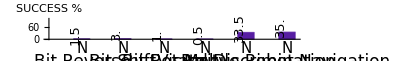

NEAT_INDIRECT.pdf

```mathematica
parts = 1;
colNumber=13;
cellAll={};

selectedData=selectData[sortedData,{"PROBLEM"->{"FC","RECO","XOR","ROBOTS"}}];
(*selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];*)
cellS=plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2,ColorsNumber->colNumber]
cellC=plotAsBoxWhiskerChartPub[selectedData,"CONSTANTS_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellN=plotAsBoxWhiskerChartPub[selectedData,"NODES_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellD=plotAsBoxWhiskerChartPub[selectedData,"DEPTH_BSF",listOfDirectProblems,2.0,parts,Epilog->epilog,ImageSize->{{1400},{3200}},ColorsNumber->colNumber];
cellAll=Join[cellAll,{{Style["",FontSize->20],Grid[{{cellS},{cellC},{cellN},{cellD}}]}}];
Export["NEAT_INDIRECT.pdf",Grid[{{Style["NEAT Inirect: Success, Constants, Nodes",FontSize->25]}}~Join~{cellAll},Frame->All]]
```

```mathematica
printBooleanRanksAsTable[selectedData,"SUCCESS",3]
```

ID | GPAT.FUNCTION_IMPL | RANK
3 | NC | 13/10
1 | GP | 19/10
2 | N | 14/5